Interfacing runDM with NRopsDD

Requires runDM v1.0, as well as NRopsDD, available at this URL.

This example shows how limits from direct detection experiments can be calculated by interfacing runDM with the publicly available code, NRopsDD. We’ll assume that DM interacts with all quarks through the axial-vector current, mediated by a heavy vector particle with mass m_V:
	ℒ =1/m_V^2∑_q  χ̄ γ^μ γ^5 χ q̄ γ_μ γ^5 q.
We’ll use runDM to take into account the running from m_V to the nuclear scale, and we’ll use NRopsDD to obtain limits on m_V from LUX.

Let’s start by loading in the runDM and NRopsDD codes.

```mathematica
Get[NotebookDirectory[] <> "runDM.m"];
(*TS and Y package files from NRopsDD*)
Get[NotebookDirectory[]<>"/NROpsDD/TS.m"];
Get[NotebookDirectory[] <> "/NROpsDD/Y.m"];
```

First, let’s specify the couplings at high energy.

```mathematica
chigh = setBenchmark["QuarksAxial"];
```

Now we specify how to calculate the non-relativistic (NR) operator coefficients. The function DDCouplingsNR already includes a factor of 1/m_V^2:

```mathematica
c[N_][op_][mv_][mx_] := DDCouplingsNR[chigh, mv, mx, "axial-vector", N][[op]];
```

Now we specify how to calculate the benchmark coupling constant λ_Bfrom the NR coefficients in the case of the LUX experiment (see arXiv:1307.5955 for more details):

```mathematica
Olist = {4, 8, 9}; (*Relevant operators for axial-vector current DM int*)
λB[mv_?NumericQ, mx_?NumericQ]:= Sqrt[Sum[c[N1][op1][mv][mx]*c[N2][op2][mv][mx]*Y["Contact"]["LUX"][op1, op2][N1,N2][mx], {N1, {"p", "n"}}, {N2, {"p", "n"}}, {op1, Olist}, {op2, Olist}]];
```

Now plot a 90% contour from the LUX experiment:

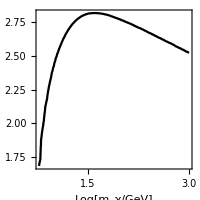

```mathematica
ContourPlot[TS["LUX"][lmx, Log10[λB[10^lmv, 10^lmx ]]]==2.71,{lmx,Log10[6],3},{lmv,0,4},
ImageSize->200,PlotRange->All,ContourStyle->Black,
FrameLabel->{"Log[m_χ/GeV]","Log_10[m_V/GeV]"}]
```